```mathematica
Get["toy2D`"]//Quiet
```

## train network

NetInformation::obsalt: NetInformation is obsolete. Instead, use Information.

General::stop: Further output of NetInformation::obsalt will be suppressed during this calculation.

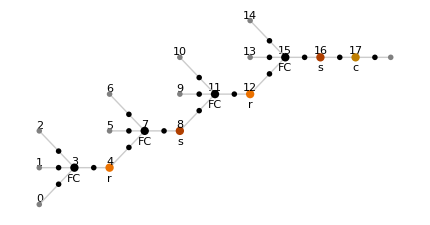
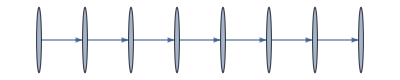
{NetChain[<>],0.603225,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{net=NetInitialize@NetChain[{100,Ramp,1000,LogisticSigmoid,1000,Ramp,1,LogisticSigmoid},"Input"->2,"Output"->NetDecoder["Scalar"]],net[{1,1}],NetInformation[net,"MXNetNodeGraphPlot"],NetInformation[net,"SummaryGraphic"],NetInformation[net,"LayersGraph"]}
```

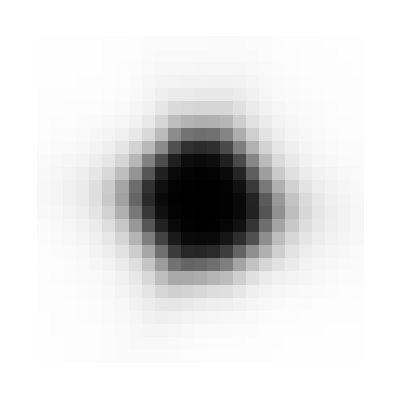
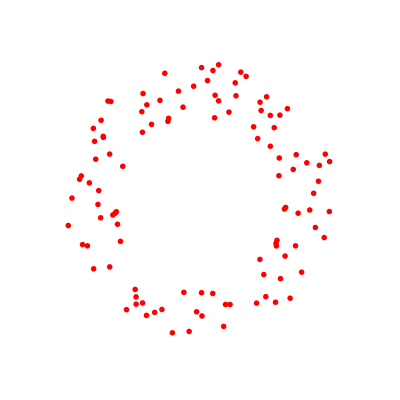

```mathematica
trained=NetTrain[net,data2,MaxTrainingRounds->Quantity[20,"Seconds"],Method->{"SGD","LearningRate"->0.003},TargetDevice->{"GPU",3},TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.1}];
f=trained;
o
```

```mathematica
plotSolution2[net_,t_]:=Style[Grid[{{Plot3D[net[{x,y}],{x,-6,6},{y,-6,6},PerformanceGoal->"Speed",PlotLabel->t],Overlay[{k[net],l,Style[t,Red,Bold,FontSize->24]}]}}],ImageSizeMultipliers->{0.9,0.9}]
(*Show[{Plot3D[net[{x,y}],{x,-6,6},{y,-6,6},PerformanceGoal->"Quality",PlotLabel->t],g,moleculePlot[ones]}]*)
```

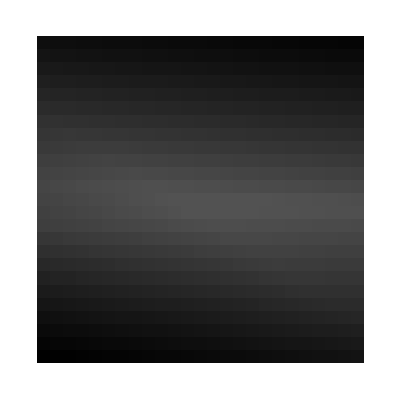
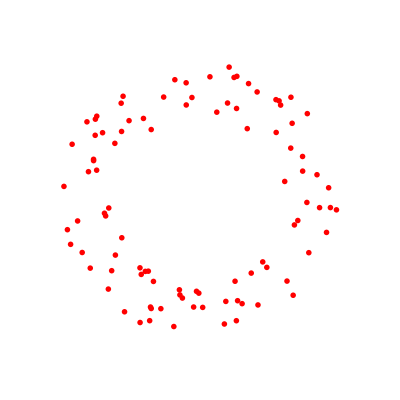
-Graphics3D- | -Graphics--Graphics-1

```mathematica
trained=NetTrain[net,data,MaxTrainingRounds->Quantity[300,"Seconds"],Method->{"SGD","LearningRate"->0.01},TargetDevice->{"GPU",3},TrainingProgressReporting->{plotSolution2[#Net,#AbsoluteBatch]&,"Interval"->0.1}];
f=trained;plotSolution2[f,1]
```

```mathematica
f=NetTrain[net,data,MaxTrainingRounds->1000,Method->{"SGD","LearningRate"->0.01}]
```

NetChain[<>]

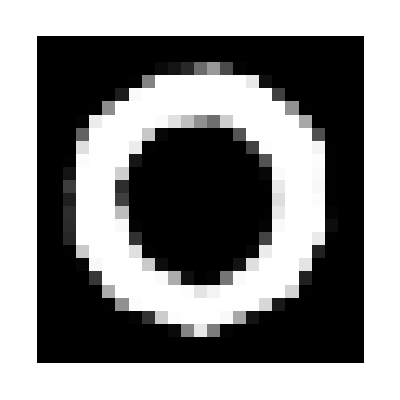
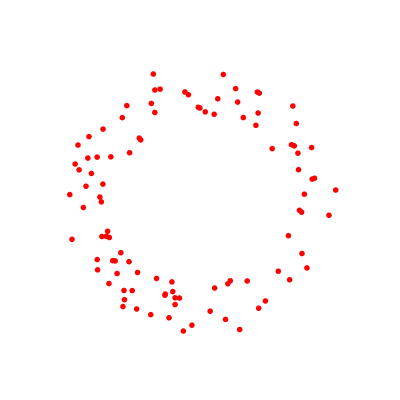

```mathematica
o
```

```mathematica
Plot3D[f[{x,y}],{x,-6,6},{y,-6,6}]
```

-Graphics3D-

```mathematica
moleculePlot[poiints_]:=Show[Graphics3D[{Translate[GraphicsComplex[{{0.0115361,-0.00644059,-0.0023318},{-6.98724,109.314,19.6968},{-53.4044,-24.1997,-94.6041},{-46.6211,-55.8814,84.2109},{107.001,-29.2263,-9.30131},{-3.48785195,54.653779705,9.8472341},{-26.69643195,-12.103070295,-47.303215900000005},{-23.30478195,-27.943920295,42.104284099999994},{53.50626805,-14.616370295,-4.651820900000001}},{{RGBColor[0.65,0.7,0.7],Sphere[2,24.],Sphere[3,24.],Sphere[4,24.],Sphere[5,24.]},{RGBColor[0.4,0.4,0.4],Sphere[1,34.]},{RGBColor[0.65,0.7,0.7],Cylinder[{6,2},15.],Cylinder[{7,3},15.],Cylinder[{8,4},15.],Cylinder[{9,5},15.]},{RGBColor[0.4,0.4,0.4],Cylinder[{1,6},15.],Cylinder[{1,7},15.],Cylinder[{1,8},15.],Cylinder[{1,9},15.]}}],#]}]&/@(500*poiints),g];
```

```mathematica
ones=Cases[data,a_/;Last[a]==1]/.Rule[{a_,b_},cc_]:>{a,b,cc};
zeros=Cases[data,a_/;Last[a]==0]/.Rule[{a_,b_},cc_]:>{a,b,cc};
```

```mathematica
Show[{Plot3D[f[{x,y}],{x,-6,6},{y,-6,6}],g,moleculePlot[ones]}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics3D-,g,Show[{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},g]}]

```mathematica
g
```

g

```mathematica
g=Graphics3D[Sphere[#,.1]&/@zeros,PlotRange->{{-6,6},{-6,6},{0,1}},]
```

-Graphics3D-

```mathematica
moleculePlot[ones_]:=Graphics3D[

{
Translate[GraphicsComplex[{
{0.0115361,-0.00644059,-0.0023318},
{-6.98724,109.314,19.6968},
{-53.4044,-24.1997,-94.6041},
{-46.6211,-55.8814,84.2109},
{107.001,-29.2263,-9.30131},
{-3.48785195,54.653779705,9.8472341},
{-26.69643195,-12.103070295,-47.303215900000005},
{-23.30478195,-27.943920295,42.104284099999994},
{53.50626805,-14.616370295,-4.651820900000001}},{{RGBColor[0.65,0.7,0.7],Sphere[2,24.],Sphere[3,24.],Sphere[4,24.],Sphere[5,24.]},{RGBColor[0.4,0.4,0.4],Sphere[1,34.]},{RGBColor[0.65,0.7,0.7],Cylinder[{6,2},15.],Cylinder[{7,3},15.],Cylinder[{8,4},15.],Cylinder[{9,5},15.]},{RGBColor[0.4,0.4,0.4],Cylinder[{1,6},15.],Cylinder[{1,7},15.],Cylinder[{1,8},15.],Cylinder[{1,9},15.]}}],#]}&/@(500ones)];
```

```mathematica
moleculePlot[ones]
```

-Graphics3D-